```mathematica
Λ=1;
M=1;
```

```mathematica
Veff[g_,Λ_,M_,x_]=-4*Pi*g/(Λ*M)*(SphericalBesselJ[0,x])^2/(1+g*x*SphericalBesselY[0,x]*SphericalBesselJ[0,x])
```

-(4 g π SphericalBesselJ[0,x]^2)/(M Λ (1+g x SphericalBesselJ[0,x] SphericalBesselY[0,x]))

```mathematica
ComplexPlot3D[Veff[1.1,1,1,x],{x,-5-2.5I,5+2.5I},PlotLegends->Automatic]
```

-Graphics3D-

```mathematica
Clear[x0]
result=FindRoot[1/Veff[1.1,1,1,x],{x,1}]
xroot = x/.result
```

{x→0.374493}

0.374493

```mathematica
y=(8*Pi*Λ/M^2)(x0 *(Sin[x0])^2)/(x0*Cos[2x0]-0.5*Sin[2x0])
```

(8 π x0 Λ Sin[x0]^2)/(M^2 (x0 Cos[2 x0]-0.5 Sin[2 x0]))

```mathematica
Δ=Λ^2x0^2/M
```

(x0^2 Λ^2)/M

19.0311/(-0.140245+x^2)-(13.823 SphericalBesselJ[0,x]^2)/(1+1.1 x SphericalBesselJ[0,x] SphericalBesselY[0,x])

-Graphics3D-

```mathematica
Needs["NumericalCalculus`"]
NResidue[Veff[1.1,1,1,x],{x,xroot}]
Residue[y/((1)^2x^2/(1)-Δ),{x,xroot}]
```

-25.4092+3.21589×10^-15 ⅈ

0

```mathematica
ComplexPlot3D[(x-xroot)*Veff[1.1,1,1,x],{x,-1-0.5I,1+0.5I},PlotLegends->Automatic]
```

-Graphics3D-

```mathematica
Ccoeff[g_,x0_,Λ_,M_,x_]=-(8 π x0 Λ Sin[x0]^2)/(M^2 ((x^2 Λ^2)/M-(x0^2 Λ^2)/M) (x0 Cos[2 x0]-0.5Sin[2 x0]))-(4 g π SphericalBesselJ[0,x]^2)/(M Λ (1+g x SphericalBesselJ[0,x] SphericalBesselY[0,x]))
```

-(8 π x0 Λ Sin[x0]^2)/(M^2 ((x^2 Λ^2)/M-(x0^2 Λ^2)/M) (x0 Cos[2 x0]-0.5 Sin[2 x0]))-(4 g π SphericalBesselJ[0,x]^2)/(M Λ (1+g x SphericalBesselJ[0,x] SphericalBesselY[0,x]))

```mathematica
Ccoeff[g,y,Δ,x]
```

-(8 π x0 Λ Sin[x0]^2)/(M^2 ((x^2 Λ^2)/M-(x0^2 Λ^2)/M) (x0 Cos[2 x0]-0.5 Sin[2 x0]))-(4 g π SphericalBesselJ[0,x]^2)/(M Λ (1+g x SphericalBesselJ[0,x] SphericalBesselY[0,x]))

```mathematica
f[x_]=Ccoeff[1.1,xroot,1,1,x]
```

19.0311/(-0.140245+x^2)-(13.823 SphericalBesselJ[0,x]^2)/(1+1.1 x SphericalBesselJ[0,x] SphericalBesselY[0,x])

```mathematica
ComplexPlot3D[f[x],{x,-6-3I,6+3I},PlotLegends->Automatic]
```

-Graphics3D-

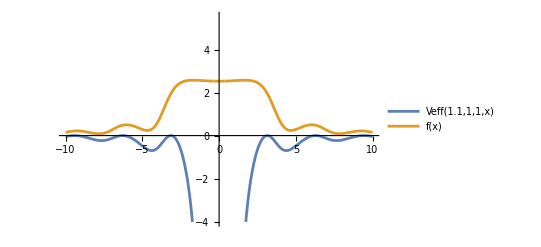

```mathematica
Plot[{Veff[1.1,1,1,x],f[x]},{x,-10,10},PlotLegends->"Expressions"]
```

```mathematica
Series[Ccoeff[g,x0,Λ,M,x],{x,0,4}]
f0[g_,x0_,Λ_,M_,x_]= Normal[Series[Ccoeff[g,x0,Λ,M,x],{x,0,0}]];
f2[g_,x0_,Λ_,M_,x_]= Normal[Series[Ccoeff[g,x0,Λ,M,x],{x,0,2}]];
f4[g_,x0_,Λ_,M_,x_]= Normal[Series[Ccoeff[g,x0,Λ,M,x],{x,0,4}]];
f6[g_,x0_,Λ_,M_,x_]= Normal[Series[Ccoeff[g,x0,Λ,M,x],{x,0,6}]];
f8[g_,x0_,Λ_,M_,x_]= Normal[Series[Ccoeff[g,x0,Λ,M,x],{x,0,8}]];
```

((4 g π)/((-1+g) M Λ)+(25.1327 Sin[x0]^2)/(M x0 Λ (x0 Cos[2 x0]-0.5 Sin[2 x0])))+((4 g (1+g) π)/(3 (-1+g)^2 M Λ)+(25.1327 Sin[x0]^2)/(M x0^3 Λ (x0 Cos[2 x0]-0.5 Sin[2 x0]))) x^2+((8 g (1+6 g+3 g^2) π)/(45 (-1+g)^3 M Λ)+(25.1327 Sin[x0]^2)/(M x0^5 Λ (x0 Cos[2 x0]-0.5 Sin[2 x0]))) x^4+O[x]^5

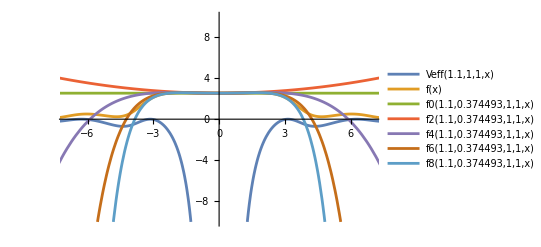

```mathematica
Plot[{Veff[1.1,1,1,x],f[x],f0[1.1,xroot,1,1,x],f2[1.1,xroot,1,1,x],f4[1.1,xroot,1,1,x],f6[1.1,xroot,1,1,x],f8[1.1,xroot,1,1,x]},{x,-10,10},PlotRange->{{-7,7},{-10,10}},PlotLegends->"Expressions"]
```

```mathematica
f6[g,x0,1,1,x]
```

(4 g π)/(-1+g)+x^6 (-4 g (-1/(315 (1-g))-(4 g)/(135 (-1+g)^2)-((2 g)/(15 (1-g))+(4 g^2)/(9 (1-g)^2))/(3 (1-g))+(-(4 g)/(315 (1-g))-(8 g^2)/(45 (1-g)^2)-(8 g^3)/(27 (1-g)^3))/(1-g)) π+(8 π Sin[x0]^2)/(x0^7 (x0 Cos[2 x0]-0.5 Sin[2 x0])))+x^4 (-4 g (2/(45 (1-g))+(2 g)/(9 (-1+g)^2)+((2 g)/(15 (1-g))+(4 g^2)/(9 (1-g)^2))/(1-g)) π+(8 π Sin[x0]^2)/(x0^5 (x0 Cos[2 x0]-0.5 Sin[2 x0])))+x^2 ((4 g (1+g) π)/(3 (-1+g)^2)+(25.1327 Sin[x0]^2)/(x0^3 (x0 Cos[2 x0]-0.5 Sin[2 x0])))+(25.1327 Sin[x0]^2)/(x0 (x0 Cos[2 x0]-0.5 Sin[2 x0]))